Piecewise[{{8.85551 ⅇ^(-1.34963 x), x>3}, {8.85551 ⅇ^(1.34963 x), x≤-3}, {0.517023 Cos[0.422476 x], True}}]

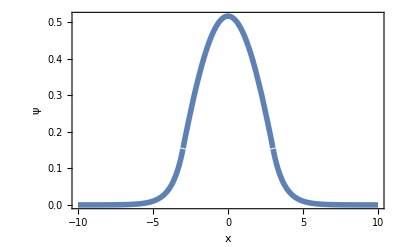

Piecewise[{{9.19332 ⅇ^(-1.14045 x), x>3}, {-9.19332 ⅇ^(1.14045 x), x≤-3}, {0.507879 Sin[0.836289 x], True}}]

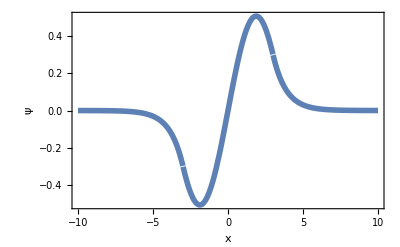

Piecewise[{{-3.47226 ⅇ^(-0.710646 x), x>3}, {-3.47226 ⅇ^(0.710646 x), x≤-3}, {0.476343 Cos[1.22269 x], True}}]

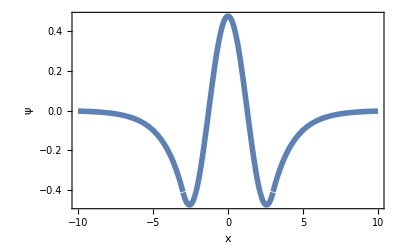

```mathematica
Clear["Global`*"]
V0=1;
m=1;
a=3;
(*参数赋值*)
q[E0_]=Sqrt[2m(V0+E0)];
k[E0_]=Sqrt[-2m*E0];
B0[E0_]=Exp[k[E0]*a]*Cos[q[E0]*a];
D0[E0_]=-Exp[k[E0]*a]*Sin[q[E0]*a];
(*已知条件带入*)
Uevenc[E0_,x_]=Cos[q[E0]*x];
Uevenp[E0_,x_]=B0[E0]*Exp[-k[E0]*x];
Uevenn[E0_,x_]=B0[E0]*Exp[k[E0]*x];
Uoddc[E0_,x_]=Sin[q[E0]*x];
Uoddp[E0_,x_]=-D0[E0]*Exp[-k[E0]*x];
Uoddn[E0_,x_]=D0[E0]*Exp[k[E0]*x];
(*写出通解*)
soleven=Flatten[FindRoot[(D[Uevenc[E0,x],x]/.x->a)==(D[Uevenp[E0,x],x]/.x->a)//Simplify,{E0,#}]&/@(Range[1,10,1]*(-10^-1))];
solodd=Flatten[FindRoot[(D[Uoddc[E0,x],x]/.x->a)==(D[Uoddp[E0,x],x]/.x->a)//Simplify,{E0,#}]&/@(Range[1,10,1]*(-10^-1))];
(*带入边界条件，求解超越方程*)
E3=E0/.soleven[[1]];
E2=E0/.solodd[[3]];
E1=E0/.soleven[[7]];
(*本征值能量获取*)
U1[x_]=Piecewise[{{Uevenn[E1,x],x<=-a},{Uevenc[E1,x],-a<x<=a},{Uevenp[E1,x],x>a}}];
U2[x_]=Piecewise[{{Uoddn[E2,x],x<=-a},{Uoddc[E2,x],-a<x<=a},{Uoddp[E2,x],x>a}}];
U3[x_]=Piecewise[{{Uevenn[E3,x],x<=-a},{Uevenc[E3,x],-a<x<=a},{Uevenp[E3,x],x>a}}];
(*带入参数，获得未归一化波函数*)
A1=Integrate[U1[x]*U1[x],{x,-Infinity,+Infinity}];
A2=Integrate[U2[x]*U2[x],{x,-Infinity,+Infinity}];
A3=Integrate[U3[x]*U3[x],{x,-Infinity,+Infinity}];
(*计算归一化因子*)
U10[x_]=PiecewiseExpand[U1[x]/(Sqrt[A1])]
(*归一化*)
Plot[U10[x],{x,-10,10},PlotStyle->Thickness[0.01],Frame->True,FrameLabel->{Style["x",18],Style["ψ",18]},FrameStyle->Thickness[0.003],PlotLegends->Style[ToString[E1]"=E1",18]]
(*绘图*)
U20[x_]=PiecewiseExpand[U2[x]/(Sqrt[A2])]
(*归一化*)

Plot[U20[x],{x,-10,10},PlotStyle->Thickness[0.01],Frame->True,FrameLabel->{Style["x",18],Style["ψ",18]},FrameStyle->Thickness[0.003],PlotLegends->Style[ToString[E2]"=E2",18]]
(*绘图*)
U30[x_]=PiecewiseExpand[U3[x]/(Sqrt[A3])]
(*归一化*)
Plot[U30[x],{x,-10,10},PlotStyle->Thickness[0.01],Frame->True,FrameLabel->{Style["x",18],Style["ψ",18]},FrameStyle->Thickness[0.003],PlotLegends->Style[ToString[E3]"=E3",18]]
(*绘图*)
```